```mathematica
SetDirectory[NotebookDirectory[]];
```

# Branching & Annihilation random walk (BARW): A->A+A & A+A->0 & Diffusion

## Import Gillespie

```mathematica
<<GillespieLattice1D`
```

## Extra functions

Moments from analytic form of partition function

```mathematica
fMomentsFromhj[h_,j_,nChain_]:={
(E^-j (2+E^j (-1+E^(h+j) (1+Sqrt[E^(-2 (h+j)) (1+E^h (4+E^j (-2+E^(h+j))))]))) nChain)/(Sqrt[E^(-2 (h+j)) (1+E^h (4+E^j (-2+E^(h+j))))] (1+E^(h+j) (1+Sqrt[E^(-2 (h+j)) (1+E^h (4+E^j (-2+E^(h+j))))])))
,
((-1+E^(h+j) (1+Sqrt[E^(-2 (h+j)) (1+E^h (4+E^j (-2+E^(h+j))))])) nChain)/(Sqrt[E^(-2 (h+j)) (1+E^h (4+E^j (-2+E^(h+j))))] (1+E^(h+j) (1+Sqrt[E^(-2 (h+j)) (1+E^h (4+E^j (-2+E^(h+j))))])))
}//N;
```

## Stochastic simulations for moments

Read/Write Flag

```mathematica
readFlag=True;
```

Parameters

```mathematica
tMax=1.0;
dt=0.01;
nChain=100;
```

### Best: branching = 10, annihilation prob = 0.1 ie also 10 for dt = 0.01

```mathematica
kBranching=10.0;
```

```mathematica
probAnnihilation=0.1;
```

```mathematica
h0=1.0;
j0=0.0;
```

```mathematica
nTrials=500;
```

Reactions

```mathematica
If[
!readFlag,
uniRxnList={fReactionUnimol["Branching",kBranching,{"A"},{"A","A"}]};
biRxnList={fReactionBimol["Annihilation",probAnnihilation,{"A","A"},{}]};
];
```

IC

```mathematica
(* Moments *)
```

```mathematica
If[
!readFlag,
fMomentsFromhj[h0,j0,nChain]
]
```

```mathematica
(* Generate initial lattice *)
```

```mathematica
If[
!readFlag,
hDict=<|"A"->h0|>;
jDict=<|{"A","A"}->j0|>;
lattice0=fGenLattice[hDict,jDict,nChain,1000];
];
```

```mathematica
(* Find the true initial h,J from lattice0 *)
```

```mathematica
If[
!readFlag,
h0j0True=FindRoot[fMomentsFromhj[h,j,nChain][[1]]==fMean[lattice0]&&fMomentsFromhj[h,j,nChain][[2]]==fNN[lattice0],{h,h0},{j,j0}]
]
```

```mathematica
If[
!readFlag,
h0=h/.h0j0True;
];
```

```mathematica
If[
!readFlag,
j0=j/.h0j0True;
];
```

```mathematica
(* Moments now *)
```

```mathematica
If[
!readFlag,
fMomentsFromhj[h0,j0,nChain]
]
```

```mathematica
If[
!readFlag,
fMean[lattice0]
]
```

```mathematica
If[
!readFlag,
fNN[lattice0]
]
```

Run

```mathematica
(* Do some number of trials*)
If[
!readFlag,

meanSt=Association[];
nnSt=Association[];
latticeSt=Association[];
Monitor[
Do[
(* Do it *)
latticeSt[iTrial]=fGillespie[tMax,dt,lattice0,uniRxnList,biRxnList];

(* Calculate mean, NN *)
meanSt[iTrial]=Table[fMean[latticeSt[iTrial][t]],{t,Keys[latticeSt[iTrial]]}];
nnSt[iTrial]=Table[fNN[latticeSt[iTrial][t]],{t,Keys[latticeSt[iTrial]]}];
,{iTrial,nTrials}];
,
ProgressIndicator[iTrial,{1,nTrials}]
];

]
```

```mathematica
(* Convert to correct format;
1 for particle, 0 otherwise;
dimensions;
nTrials x time x nChain
*)
```

```mathematica
If[
!readFlag,

trainingData={};
Do[
AppendTo[
trainingData
,
Table[Map[If[#=!=0,1,0]&,latticeSt[iTrial][iTime]],{iTime,Keys[latticeSt[iTrial]]}]
];
,{iTrial,Keys[latticeSt]}];

];
```

```mathematica
If[
!readFlag,
Dimensions[trainingData]
]
```

Write

```mathematica
If[
!readFlag,
Export[NotebookDirectory[]<>"trainingData.dat",trainingData];
tmp=Transpose[{Keys[meanSt],Values[meanSt]}];
tmp[[;;,1]]=Table[{tmp[[i,1]]},{i,1,Length[tmp]}];
tmp=Table[Flatten[tmp[[i]]],{i,1,Length[tmp]}];
Export[NotebookDirectory[]<>"meanSt.dat",tmp];
tmp=Transpose[{Keys[nnSt],Values[nnSt]}];
tmp[[;;,1]]=Table[{tmp[[i,1]]},{i,1,Length[tmp]}];
tmp=Table[Flatten[tmp[[i]]],{i,1,Length[tmp]}];
Export[NotebookDirectory[]<>"nnSt.dat",tmp];
Export[NotebookDirectory[]<>"h0j0.dat",{h0,j0}];
];
```

Alternatively, read

```mathematica
readFlag=True
```

True

```mathematica
If[
readFlag,
trainingData=Import[NotebookDirectory[]<>"trainingData.dat","Table"];
meanSt=Import[NotebookDirectory[]<>"meanSt.dat","Table"];
nnSt=Import[NotebookDirectory[]<>"nnSt.dat","Table"];
{h0,j0}=Import[NotebookDirectory[]<>"h0j0.dat","Table"];
h0=h0[[1]];
j0=j0[[1]];
];
```

```mathematica
meanStAss=Association[];
Do[
meanStAss[meanSt[[i,1]]]=meanSt[[i,2;;]];
,{i,1,Length[meanSt]}];
nnStAss=Association[];
Do[
nnStAss[nnSt[[i,1]]]=nnSt[[i,2;;]];
,{i,1,Length[nnSt]}];
meanSt=meanStAss;
nnSt=nnStAss;
```

Plot

```mathematica
(* Average mean, NN *)
```

```mathematica
meanAve=Mean[Values[meanSt]]//N;
nnAve=Mean[Values[nnSt]]//N;
```

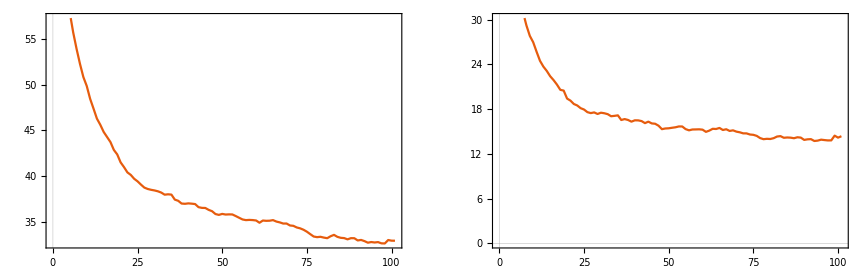

```mathematica
GraphicsRow[{
ListLinePlot[meanAve],
ListLinePlot[nnAve]
}]
```

## Functions to solve the BMLA

All the basis funcs

```mathematica
dhdtAnn[h_,j_]:=1/2 ⅇ^-h (-1+ⅇ^h (-4+3 ⅇ^j)) (-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))) ;
djdtAnn[h_,j_]:=-(-1+ⅇ^j) (-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))));
```

```mathematica
dhdtBran[h_,j_]:=-1/2 ⅇ^-h (1+ⅇ^h (6+ⅇ^j (-4-√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))+ⅇ^h (-2+3 ⅇ^j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))));
djdtBran[h_,j_]:=(ⅇ^(-h-j)  (1+ⅇ^(2 (h+j)) (7+2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^h (2+ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-4 ⅇ^(2 (h+j)) Cosh[j]))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))));
```

```mathematica
dhdtDiff[h_,j_]:=(8  ⅇ^h (-1+ⅇ^j))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))));
djdtDiff[h_,j_]:=-(4 ⅇ^-j (-1+ⅇ^j) (1+ⅇ^(h+j)))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))));
```

```mathematica
dhdtBimolAnn[h_,j_]:=-((4 ⅇ^(2 h+j) (2+11 ⅇ^h+13 ⅇ^(2 h)-ⅇ^j-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) )/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))));
djdtBimolAnn[h_,j_]:=(2 (-1-7 ⅇ^h-14 ⅇ^(2 h)-7 ⅇ^(3 h)-2 ⅇ^(2 (h+j))-2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+3 ⅇ^(4 h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 h+j) (2-5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+j) (-10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(8 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(5 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(6 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 h+2 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+5 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 h+j) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 (h+j)) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+2 j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(7 h+6 j) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (7+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) )/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
dhdtFra[h_,j_]:=(2 ⅇ^(h+j) (1+5 ⅇ^h+3 ⅇ^(2 h)-6 ⅇ^(3 h)+2 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) )/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
djdtFra[h_,j_]:=-((2 (1+7 ⅇ^h+14 ⅇ^(2 h)+7 ⅇ^(3 h)+ⅇ^(h+j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(7 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 h+6 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+2 j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+2 j) (7+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+4 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+j) (8+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (14+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (6+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+5 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) )/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))) ;
```

```mathematica
fBFs[h_,j_]:={
{dhdtAnn[h,j],dhdtBran[h,j],dhdtDiff[h,j],dhdtBimolAnn[h,j],dhdtFra[h,j]},{djdtAnn[h,j],djdtBran[h,j],djdtDiff[h,j],djdtBimolAnn[h,j],djdtFra[h,j]}
}//N;
```

```mathematica
fBFsRed[h_,j_]:={
{dhdtBran[h,j],dhdtDiff[h,j],dhdtBimolAnn[h,j]},
{djdtBran[h,j],djdtDiff[h,j],djdtBimolAnn[h,j]}
}//N;
```

All the derivatives of the basis funcs

```mathematica
dhdtAnndh[h_,j_]:=1/2 (-4+3 ⅇ^j) (-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-1/2 ⅇ^-h (-1+ⅇ^h (-4+3 ⅇ^j)) (-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))+1/2 ⅇ^-h (-1+ⅇ^h (-4+3 ⅇ^j)) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))+ⅇ^(-2 (h+j)) (ⅇ^(2 h+2 j)+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))));
dhdtAnndj[h_,j_]:=3/2 ⅇ^j (-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))+1/2 ⅇ^-h (-1+ⅇ^h (-4+3 ⅇ^j)) ((ⅇ^(h+j) (ⅇ^(h-2 (h+j)) (ⅇ^(h+2 j)+ⅇ^j (-2+ⅇ^(h+j)))-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))));
```

```mathematica
djdtAnndh[h_,j_]:=(1-ⅇ^j) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))+ⅇ^(-2 (h+j)) (ⅇ^(2 h+2 j)+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))));
djdtAnndj[h_,j_]:=-ⅇ^j (-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))+(1-ⅇ^j) ((ⅇ^(h+j) (ⅇ^(h-2 (h+j)) (ⅇ^(h+2 j)+ⅇ^j (-2+ⅇ^(h+j)))-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))));
```

```mathematica
dhdtBrandh[h_,j_]:=1/2 ⅇ^-h (1+ⅇ^h (6+ⅇ^j (-4-√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))+ⅇ^h (-2+3 ⅇ^j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))))-1/2 ⅇ^-h (ⅇ^(h+j) (ⅇ^h (-2+3 ⅇ^j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))-(-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))+ⅇ^(-2 (h+j)) (ⅇ^(2 h+2 j)+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+(ⅇ^h (-2+3 ⅇ^j) (-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))+ⅇ^(-2 (h+j)) (ⅇ^(2 h+2 j)+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))+ⅇ^h (6+ⅇ^j (-4-√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))+ⅇ^h (-2+3 ⅇ^j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))));
dhdtBrandj[h_,j_]:=1/2 (-ⅇ^j (-(ⅇ^(h-2 (h+j)) (ⅇ^(h+2 j)+ⅇ^j (-2+ⅇ^(h+j)))-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+(ⅇ^h (-2+3 ⅇ^j) (ⅇ^(h-2 (h+j)) (ⅇ^(h+2 j)+ⅇ^j (-2+ⅇ^(h+j)))-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+3 ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-ⅇ^j (-4-√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))+ⅇ^h (-2+3 ⅇ^j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))));
```

```mathematica
djdtBrandh[h_,j_]:=(ⅇ^(-h-j) (2 ⅇ^(2 (h+j)) (7+2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+(ⅇ^(2 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))+ⅇ^(-2 (h+j)) (ⅇ^(2 h+2 j)+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^h (2+ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))+ⅇ^h (2 ⅇ^(j+2 (h+j)) (-1+2 ⅇ^j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+(ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))+ⅇ^(-2 (h+j)) (ⅇ^(2 h+2 j)+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-8 ⅇ^(2 (h+j)) Cosh[j]))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-(ⅇ^(-h-j) (1+ⅇ^(2 (h+j)) (7+2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^h (2+ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-4 ⅇ^(2 (h+j)) Cosh[j]))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-(ⅇ^(-h-j) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))+ⅇ^(-2 (h+j)) (ⅇ^(2 h+2 j)+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))) (1+ⅇ^(2 (h+j)) (7+2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^h (2+ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-4 ⅇ^(2 (h+j)) Cosh[j]))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))^2;
```

```mathematica
djdtBrandj[h_,j_]:=-((ⅇ^(-h-j) (1+ⅇ^(2 (h+j)) (7+2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^h (2+ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-4 ⅇ^(2 (h+j)) Cosh[j]))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))))-(ⅇ^(-h-j) ((ⅇ^(h+j) (ⅇ^(h-2 (h+j)) (ⅇ^(h+2 j)+ⅇ^j (-2+ⅇ^(h+j)))-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))) (1+ⅇ^(2 (h+j)) (7+2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^h (2+ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-4 ⅇ^(2 (h+j)) Cosh[j]))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))^2+(ⅇ^(-h-j) ((ⅇ^(2 (h+j)) (ⅇ^(h-2 (h+j)) (ⅇ^(h+2 j)+ⅇ^j (-2+ⅇ^(h+j)))-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+2 ⅇ^(2 (h+j)) (7+2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^h ((ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (ⅇ^(h-2 (h+j)) (ⅇ^(h+2 j)+ⅇ^j (-2+ⅇ^(h+j)))-2 ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))/(2 √(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^j (1+ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))+ⅇ^j (2 ⅇ^(j+2 (h+j))+2 ⅇ^(2 (h+j)) (-1+2 ⅇ^j)) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))-8 ⅇ^(2 (h+j)) Cosh[j]-4 ⅇ^(2 (h+j)) Sinh[j]))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))));
```

```mathematica
dhdtDiffdh[h_,j_]:=(8 ⅇ^h (-1+ⅇ^j))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))-(8 ⅇ^h (-1+ⅇ^j) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2);
```

```mathematica
dhdtDiffdj[h_,j_]:=(8 ⅇ^(h+j))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))-(8 ⅇ^h (-1+ⅇ^j) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2);
```

```mathematica
djdtDiffdh[h_,j_]:=-(4 ⅇ^h (-1+ⅇ^j))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))+(4 ⅇ^-j (-1+ⅇ^j) (1+ⅇ^(h+j)) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2;
```

```mathematica
djdtDiffdj[h_,j_]:=-(4 ⅇ^h (-1+ⅇ^j))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))-(4 (1+ⅇ^(h+j)))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))+(4 ⅇ^-j (-1+ⅇ^j) (1+ⅇ^(h+j)))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))+(4 ⅇ^-j (-1+ⅇ^j) (1+ⅇ^(h+j)) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2;
```

```mathematica
dhdtBimolAnndh[h_,j_]:=-((8 ⅇ^(2 h+j) (2+11 ⅇ^h+13 ⅇ^(2 h)-ⅇ^j-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))))+(4 ⅇ^(2 h+j) (2+11 ⅇ^h+13 ⅇ^(2 h)-ⅇ^j-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))+(4 ⅇ^(2 h+j) (2+11 ⅇ^h+13 ⅇ^(2 h)-ⅇ^j-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (6 ⅇ^h+18 ⅇ^(2 h)+6 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+8 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)-(4 ⅇ^(2 h+j) (11 ⅇ^h+26 ⅇ^(2 h)-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-3 ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-4 ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+14 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+48 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-4 ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(2 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(5 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(2 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(6 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(5 h+6 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(6 h+7 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
dhdtBimolAnndj[h_,j_]:=-((4 ⅇ^(2 h+j) (2+11 ⅇ^h+13 ⅇ^(2 h)-ⅇ^j-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))))+(4 ⅇ^(2 h+j) (2+11 ⅇ^h+13 ⅇ^(2 h)-ⅇ^j-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))+(4 ⅇ^(2 h+j) (2+11 ⅇ^h+13 ⅇ^(2 h)-ⅇ^j-ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)-(4 ⅇ^(2 h+j) (-ⅇ^j-2 ⅇ^(h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-3 ⅇ^(2 h+3 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-4 ⅇ^(3 h+4 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-5 ⅇ^(4 h+5 j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(2 h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(6 h+7 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+36 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(2 (h+j)) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-4 ⅇ^(4 (h+j)) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (-5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-6 ⅇ^(5 h+6 j) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 (h+j)) (5+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(3 h+2 j) (4+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 (h+j)) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(2 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(5 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(2 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(6 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(5 h+6 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(6 h+7 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
djdtBimolAnndh[h_,j_]:=-((2 (-1-7 ⅇ^h-14 ⅇ^(2 h)-7 ⅇ^(3 h)-2 ⅇ^(2 (h+j))-2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+3 ⅇ^(4 h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 h+j) (2-5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+j) (-10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(8 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(5 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(6 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 h+2 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+5 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 h+j) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 (h+j)) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+2 j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(7 h+6 j) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (7+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))))-(2 (-1-7 ⅇ^h-14 ⅇ^(2 h)-7 ⅇ^(3 h)-2 ⅇ^(2 (h+j))-2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+3 ⅇ^(4 h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 h+j) (2-5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+j) (-10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(8 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(5 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(6 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 h+2 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+5 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 h+j) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 (h+j)) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+2 j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(7 h+6 j) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (7+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (6 ⅇ^h+18 ⅇ^(2 h)+6 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+8 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)+(2 (-7 ⅇ^h-28 ⅇ^(2 h)-21 ⅇ^(3 h)-4 ⅇ^(2 (h+j))-6 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-8 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-10 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-12 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+12 ⅇ^(4 h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(2 h+j) (2-5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-4 ⅇ^(4 h+j) (-10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+8 ⅇ^(8 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-20 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-25 ⅇ^(5 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+72 ⅇ^(6 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 h+2 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-6 ⅇ^(6 h+5 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-9 ⅇ^(3 h+j) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-7 ⅇ^(7 (h+j)) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+2 j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+7 ⅇ^(7 h+6 j) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+3 j) (7+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(6 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(7 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(8 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(5 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(5 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(5 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(9 ⅇ^(5 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(5 ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(6 ⅇ^(6 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(6 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(7 h+6 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
djdtBimolAnndj[h_,j_]:=-((2 (-1-7 ⅇ^h-14 ⅇ^(2 h)-7 ⅇ^(3 h)-2 ⅇ^(2 (h+j))-2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+3 ⅇ^(4 h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 h+j) (2-5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+j) (-10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(8 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(5 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(6 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 h+2 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+5 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 h+j) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 (h+j)) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+2 j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(7 h+6 j) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (7+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))))-(2 (-1-7 ⅇ^h-14 ⅇ^(2 h)-7 ⅇ^(3 h)-2 ⅇ^(2 (h+j))-2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+3 ⅇ^(4 h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 h+j) (2-5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+j) (-10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(8 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(5 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(6 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(3 h+2 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+5 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 h+j) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 (h+j)) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+2 j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(7 h+6 j) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (7+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)+(2 (-4 ⅇ^(2 (h+j))-6 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-8 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-10 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-12 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+6 ⅇ^(4 h+2 j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 h+j) (2-5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+j) (-10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+8 ⅇ^(8 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-15 ⅇ^(4 h+3 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-20 ⅇ^(5 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+48 ⅇ^(6 h+4 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(3 h+2 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(6 h+5 j) (10+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-3 ⅇ^(3 h+j) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-7 ⅇ^(7 (h+j)) (3+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(5 h+2 j) (17+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(7 h+6 j) (9+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(5 h+3 j) (7+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(6 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(7 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(8 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(5 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(5 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(5 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(9 ⅇ^(5 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(5 ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(6 ⅇ^(6 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(6 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(7 h+6 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
dhdtFradh[h_,j_]:=(2 ⅇ^(h+j) (1+5 ⅇ^h+3 ⅇ^(2 h)-6 ⅇ^(3 h)+2 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))-(2 ⅇ^(h+j) (1+5 ⅇ^h+3 ⅇ^(2 h)-6 ⅇ^(3 h)+2 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))-(2 ⅇ^(h+j) (1+5 ⅇ^h+3 ⅇ^(2 h)-6 ⅇ^(3 h)+2 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (6 ⅇ^h+18 ⅇ^(2 h)+6 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+8 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)+(2 ⅇ^(h+j) (5 ⅇ^h+6 ⅇ^(2 h)-18 ⅇ^(3 h)+4 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+6 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+8 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-3 ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-4 ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+18 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-12 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-8 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+9 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-10 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(2 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(6 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(9 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(11 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(3 ⅇ^(5 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(9 ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(6 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
dhdtFradj[h_,j_]:=(2 ⅇ^(h+j) (1+5 ⅇ^h+3 ⅇ^(2 h)-6 ⅇ^(3 h)+2 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))-(2 ⅇ^(h+j) (1+5 ⅇ^h+3 ⅇ^(2 h)-6 ⅇ^(3 h)+2 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))-(2 ⅇ^(h+j) (1+5 ⅇ^h+3 ⅇ^(2 h)-6 ⅇ^(3 h)+2 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)+(2 ⅇ^(h+j) (4 ⅇ^(2 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+6 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+8 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))-ⅇ^(3 h+j) (-14+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+2 j) (-13+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+18 ⅇ^(6 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-10 ⅇ^(6 h+5 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(2 h+j) (4+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(4 h+j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 (h+j)) (-1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(3 h+2 j) (4+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-6 ⅇ^(5 h+3 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(5 h+4 j) (17+9 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(2 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(6 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(9 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(11 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(3 ⅇ^(5 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(9 ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(6 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
djdtFradh[h_,j_]:=(2 (1+7 ⅇ^h+14 ⅇ^(2 h)+7 ⅇ^(3 h)+ⅇ^(h+j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(7 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 h+6 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+2 j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+2 j) (7+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+4 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+j) (8+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (14+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (6+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+5 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))+(2 (1+7 ⅇ^h+14 ⅇ^(2 h)+7 ⅇ^(3 h)+ⅇ^(h+j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(7 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 h+6 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+2 j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+2 j) (7+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+4 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+j) (8+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (14+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (6+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+5 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (6 ⅇ^h+18 ⅇ^(2 h)+6 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+8 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)-(2 (7 ⅇ^h+28 ⅇ^(2 h)+21 ⅇ^(3 h)+ⅇ^(h+j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+6 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+8 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+10 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+12 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(2 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+14 ⅇ^(7 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-7 ⅇ^(7 h+6 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-5 ⅇ^(5 h+2 j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+12 ⅇ^(4 h+2 j) (7+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-6 ⅇ^(6 h+4 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(3 h+j) (8+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+3 j) (14+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(2 h+j) (6+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(3 h+2 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(6 h+5 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(5 h+4 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(2 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(6 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(7 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(5 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(5 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(11 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(5 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(11 ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(3 ⅇ^(6 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(6 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(7 h+6 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (4 ⅇ^h-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
djdtFradj[h_,j_]:=(2 (1+7 ⅇ^h+14 ⅇ^(2 h)+7 ⅇ^(3 h)+ⅇ^(h+j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(7 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 h+6 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+2 j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+2 j) (7+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+4 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+j) (8+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (14+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (6+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+5 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2 (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))+(2 (1+7 ⅇ^h+14 ⅇ^(2 h)+7 ⅇ^(3 h)+ⅇ^(h+j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+ⅇ^(2 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(7 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(7 h+6 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(5 h+2 j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+2 j) (7+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-ⅇ^(6 h+4 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+j) (8+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+3 j) (14+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (6+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(6 h+5 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(2 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))^2)-(2 (ⅇ^(h+j) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+6 ⅇ^(3 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+8 ⅇ^(4 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+10 ⅇ^(5 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+12 ⅇ^(6 (h+j)) √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))+2 ⅇ^(2 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+14 ⅇ^(7 (h+j)) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-6 ⅇ^(7 h+6 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-2 ⅇ^(5 h+2 j) (5+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+6 ⅇ^(4 h+2 j) (7+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-4 ⅇ^(6 h+4 j) (5+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+j) (8+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(5 h+3 j) (14+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (6+5 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(3 h+2 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+5 ⅇ^(6 h+5 j) (12+7 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+3 ⅇ^(4 h+3 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+4 ⅇ^(5 h+4 j) (12+11 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(2 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(3 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(5 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(6 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(7 (h+j)) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(5 ⅇ^(2 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(3 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(ⅇ^(4 h+j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(3 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(4 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(5 h+2 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(11 ⅇ^(4 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(3 ⅇ^(5 h+3 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(11 ⅇ^(5 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(3 ⅇ^(6 h+4 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+(7 ⅇ^(6 h+5 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))-(ⅇ^(7 h+6 j) (-2 ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))+ⅇ^(-2 (h+j)) (-2 ⅇ^(h+j)+2 ⅇ^(2 (h+j)))))/(2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))))/((1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))) (1+6 ⅇ^h+9 ⅇ^(2 h)+2 ⅇ^(3 h)+ⅇ^(h+j) (-1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(5 h+4 j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+2 ⅇ^(4 h+2 j) (2+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(4 h+3 j) (1+2 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+2 j) (1+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(3 h+j) (7+3 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))+ⅇ^(2 h+j) (1+4 √(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))));
```

```mathematica
fBFsDerivs[hVal_,jVal_]:={
{dhdtAnndh[hVal,jVal],dhdtBrandh[hVal,jVal],dhdtDiffdh[hVal,jVal],dhdtBimolAnndh[hVal,jVal],dhdtFradh[hVal,jVal]},
{dhdtAnndj[hVal,jVal],dhdtBrandj[hVal,jVal],dhdtDiffdj[hVal,jVal],dhdtBimolAnndj[hVal,jVal],dhdtFradj[hVal,jVal]},
{djdtAnndh[hVal,jVal],djdtBrandh[hVal,jVal],djdtDiffdh[hVal,jVal],djdtBimolAnndh[hVal,jVal],djdtFradh[hVal,jVal]},
{djdtAnndj[hVal,jVal],djdtBrandj[hVal,jVal],djdtDiffdj[hVal,jVal],djdtBimolAnndj[hVal,jVal],djdtFradj[hVal,jVal]}
}//N;
```

```mathematica
fBFsDerivsRed[hVal_,jVal_]:={
{dhdtBrandh[hVal,jVal],dhdtDiffdh[hVal,jVal],dhdtBimolAnndh[hVal,jVal]},
{dhdtBrandj[hVal,jVal],dhdtDiffdj[hVal,jVal],dhdtBimolAnndj[hVal,jVal]},
{djdtBrandh[hVal,jVal],djdtDiffdh[hVal,jVal],djdtBimolAnndh[hVal,jVal]},
{djdtBrandj[hVal,jVal],djdtDiffdj[hVal,jVal],djdtBimolAnndj[hVal,jVal]}
}//N;
```

### Test

```mathematica
fBFsDerivs[1,1]
```

{{30.3533,-45.0647,0.133564,-493.143,44.9295},{81.7906,-95.7458,1.64586,-650.739,94.9067},{-25.2782,32.5752,0.0864825,246.295,-32.6005},{-60.8901,67.7578,-0.772001,322.786,-67.4562}}

Solve for trajectory of h,J

### Two thetas

```mathematica
fSolveTraj[thetah_,thetaj_,h0Val_,j0Val_,dtVal_,tMaxVal_,redFlag_:False]:=Module[
{hTraj,jTraj,bfsh,bfsj,dh,dj}
,
hTraj={h0Val};
jTraj={j0Val};
Do[
If[redFlag
,
{bfsh,bfsj}=fBFsRed[hTraj[[-1]],jTraj[[-1]]];
,
{bfsh,bfsj}=fBFs[hTraj[[-1]],jTraj[[-1]]];
];

dh=Dot[thetah,bfsh];
dj=Dot[thetaj,bfsj];

AppendTo[hTraj,hTraj[[-1]]+dtVal*dh];
AppendTo[jTraj,jTraj[[-1]]+dtVal*dj];

,{t,dtVal,tMaxVal,dtVal}];

Return[{hTraj,jTraj}]
];
```

### Test

```mathematica
thetahTest={0,0,0,0,0};
thetajTest={0,0,0,0,0};
```

```mathematica
thetahTest={0,1.0,1.0,5.0,0};
thetajTest={0,1.0,1.0,5.0,0};
```

```mathematica
{hTrajTest,jTrajTest}=fSolveTraj[thetahTest,thetajTest,h0,j0,dt,tMax];
```

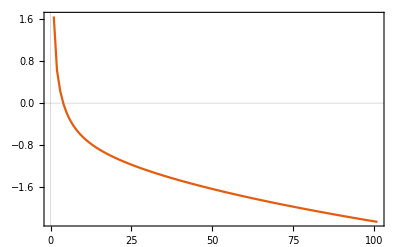

```mathematica
ListLinePlot[hTrajTest]
```

### One theta

```mathematica
fSolveTrajOneTheta[theta,h0Val,j0Val,dtVal*dtMult,tMaxVal,True]
```

fSolveTrajOneTheta[theta,h0Val,j0Val,dtMult dtVal,tMaxVal,True]

```mathematica
fSolveTrajOneTheta[theta_,h0Val_,j0Val_,dtVal_,tMaxVal_,redFlag_:False]:=Module[
{hTraj,jTraj,bfsh,bfsj,dh,dj}
,
hTraj={h0Val};
jTraj={j0Val};
Do[
If[redFlag
,
{bfsh,bfsj}=fBFsRed[hTraj[[-1]],jTraj[[-1]]];
,
{bfsh,bfsj}=fBFs[hTraj[[-1]],jTraj[[-1]]];
];

dh=Dot[theta,bfsh];
dj=Dot[theta,bfsj];

AppendTo[hTraj,hTraj[[-1]]+dtVal*dh];
AppendTo[jTraj,jTraj[[-1]]+dtVal*dj];

,{t,dtVal,tMaxVal,dtVal}];

Return[{hTraj,jTraj}]
];
```

Derivate (variational) term

### Two thetas

```mathematica
fDerivTerm[hTraj_,jTraj_,thetah_,thetaj_,dtVal_,tMaxVal_]:=Module[
{nbfs,varhWRTh,varhWRTj,varjWRTh,varjWRTj,bfs,bfsDerivs,dSumhh,dSumhj,dSumjh,dSumjj,dvarhWRTh,dvarhWRTj,dvarjWRTh,dvarjWRTj}
,
(* Number of bfs *)
nbfs=Length[thetah];

(* IC *)
varhWRTh={ConstantArray[0.0,nbfs]};
varhWRTj={ConstantArray[0.0,nbfs]};
varjWRTh={ConstantArray[0.0,nbfs]};
varjWRTj={ConstantArray[0.0,nbfs]};

(* Go *)
Do[

(* Basis funcs *)
bfs=fBFs[hTraj[[i]],jTraj[[i]]];

(* Take the derivative *)
bfsDerivs=fBFsDerivs[hTraj[[i]],jTraj[[i]]];
(* Derivative sums *)
dSumhh=Dot[thetah,bfsDerivs[[1]]];
dSumhj=Dot[thetah,bfsDerivs[[2]]];
dSumjh=Dot[thetaj,bfsDerivs[[3]]];
dSumjj=Dot[thetaj,bfsDerivs[[4]]];

(* Evaluate *)
dvarhWRTh=bfs[[1]]+varhWRTh[[-1]]*dSumhh+varjWRTh[[-1]]*dSumhj;
dvarhWRTj=varhWRTj[[-1]]*dSumhh+varjWRTj[[-1]]*dSumhj;
dvarjWRTh=varhWRTh[[-1]]*dSumjh+varjWRTh[[-1]]*dSumjj;
dvarjWRTj=bfs[[2]]+varhWRTj[[-1]]*dSumjh+varjWRTj[[-1]]*dSumjj;

(* Update *)
AppendTo[varhWRTh,varhWRTh[[-1]]+dtVal*dvarhWRTh];
AppendTo[varhWRTj,varhWRTj[[-1]]+dtVal*dvarhWRTj];
AppendTo[varjWRTh,varjWRTh[[-1]]+dtVal*dvarjWRTh];
AppendTo[varjWRTj,varjWRTj[[-1]]+dtVal*dvarjWRTj];

,{i,1,IntegerPart[tMaxVal/dtVal]}];

Return[{varhWRTh,varhWRTj,varjWRTh,varjWRTj}];
];
```

### Test

```mathematica
thetahTest={1,1,1,1,1};
thetajTest={1,1,1,1,1};
```

```mathematica
{hTrajTest,jTrajTest}=fSolveTraj[thetahTest,thetajTest,1.0,0.0,dt,tMax];
```

```mathematica
(*
fDerivTerm[hTrajTest,jTrajTest,thetahTest,thetajTest,dt,tMax]
*)
```

### One theta

```mathematica
fDerivTermOneTheta[hTraj_,jTraj_,theta_,dtVal_,tMaxVal_,redFlag_:False]:=Module[
{nbfs,varh,varj,bfs,bfsDerivs,dSumhh,dSumhj,dSumjh,dSumjj,dvarh,dvarj}
,
(* Number of bfs *)
nbfs=Length[theta];

(* IC *)
varh={ConstantArray[0.0,nbfs]};
varj={ConstantArray[0.0,nbfs]};

(* Go *)
Do[

(* Basis funcs *)
If[redFlag
,
bfs=fBFsRed[hTraj[[i]],jTraj[[i]]];
,
bfs=fBFs[hTraj[[i]],jTraj[[i]]];
];

(* Take the derivative *)
If[redFlag
,
bfsDerivs=fBFsDerivsRed[hTraj[[i]],jTraj[[i]]];
,
bfsDerivs=fBFsDerivs[hTraj[[i]],jTraj[[i]]];
];

(* Derivative sums *)
dSumhh=Dot[theta,bfsDerivs[[1]]];
dSumhj=Dot[theta,bfsDerivs[[2]]];
dSumjh=Dot[theta,bfsDerivs[[3]]];
dSumjj=Dot[theta,bfsDerivs[[4]]];

(* Evaluate *)
dvarh=bfs[[1]]+varh[[-1]]*dSumhh+varj[[-1]]*dSumhj;
dvarj=bfs[[2]]+varh[[-1]]*dSumjh+varj[[-1]]*dSumjj;

(* Update *)
AppendTo[varh,varh[[-1]]+dtVal*dvarh];
AppendTo[varj,varj[[-1]]+dtVal*dvarj];

,{i,1,IntegerPart[tMaxVal/dtVal]}];

Return[{varh,varj}];
];
```

Relate h,j to moments analytically

```mathematica
m1Analytic[h_,j_,n_]:=(ⅇ^-j (2+ⅇ^j (-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j)))))))) n)/(√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))) (1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))));
```

```mathematica
m2Analytic[h_,j_,n_]:=((-1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))) n)/(√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))) (1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+ⅇ^h (4+ⅇ^j (-2+ⅇ^(h+j))))))));
```

Boltzmann machine learning

```mathematica
(* Inputs;
s = stoch data. first dim = number trials = nTrials. Second = time. Third = lattice sites. Values = 0 or 1;
nIterBM = number iterations to run BM for;
nBatch = Batch size;
nGibbs = number steps for gibbs sampling;
h0,j0,dt,tmax,nchain;
lambda = learning rate;
*)
```

### Two thetas

```mathematica
runBM[s_,nIterBM_,nBatch_,nGibbs_,nBasis_,h0Val_,j0Val_,dtVal_,tMaxVal_,nChain_,lambdaMaxArr_,analyticFlag_,verboseFlag_]:=Module[
{nTrials,nTimePts,thetah,thetaj,thetahSt,thetajSt,hTraj,jTraj,sBatch,meanAwake,nnAwake,meanAsleep,nnAsleep,meanCurr,nnCurr,lattice,varyhWRTh,varyhWRTj,varyjWRTh,varyjWRTj,objh,objj,maxUpdate}
,
(* Number of trials, timepoints *)
nTrials = Length[s];
nTimePts=IntegerPart[tMaxVal/dtVal]+1;

(* Initial guess for theta *)
(* Order: Annihilation, Branching, Diffusion, Bimol Annihilation, Fratricide *)
thetah={0,1.0,1.0,5.0,0};
thetaj={0,1.0,1.0,5.0,0};
thetahSt={thetah};
thetajSt={thetaj};
If[verboseFlag,Print["Initial: ",Join[thetah,thetaj]];];

If[nTrials==nBatch,
(* Calculate averages now! *)
meanAwake=Table[Mean[Table[fMean[s[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];
nnAwake=Table[Mean[Table[fNN[s[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];

(* Lowpass *)
(*
meanAwake=LowpassFilter[meanAwake,0.5];
nnAwake=LowpassFilter[nnAwake,0.5];
*)
];

(* Pass over the data multiple times *)
Monitor[
Do[
If[verboseFlag,Print["Starting iter: ",iIter];];

(* Generate trajectory *)
If[verboseFlag,Print["   Generating traj..."];];
{hTraj,jTraj}=fSolveTraj[thetah,thetaj,h0Val,j0Val,dtVal,tMaxVal,True];

If[nTrials!=nBatch,
(* 
Generate a random batch;
Dimensions of s: nTrials x nTimePts x nChain;
Dimensions of sBatch: nBatch x nTimePts x nChain;
*)
sBatch=RandomSample[s,nBatch];

(* Awake phase *)
If[verboseFlag,Print["   Awake phase..."];];
meanAwake=Table[Mean[Table[fMean[sBatch[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];
nnAwake=Table[Mean[Table[fNN[sBatch[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];
];

(* Asleep phase *)
If[verboseFlag,Print["   Asleep phase..."];];
(* Go over all times *)
meanAsleep={};
nnAsleep={};
If[analyticFlag,
Do[
AppendTo[meanAsleep,m1Analytic[hTraj[[iTime]],jTraj[[iTime]],nChain]//N];
AppendTo[nnAsleep,m2Analytic[hTraj[[iTime]],jTraj[[iTime]],nChain]//N];
,{iTime,1,nTimePts}];
,
Do[
(* Make nBatch samples at this h and J *)
meanCurr={};
nnCurr={};
Do[
(* Gibbs sampling *)
lattice=fGenLattice[<|"A"->hTraj[[iTime]]|>,<|{"A","A"}->jTraj[[iTime]]|>,nChain,nGibbs,False,False];
(* Means, averages *)
AppendTo[meanCurr,fMean[lattice]];
AppendTo[nnCurr,fNN[lattice]];
,{iBatch,nBatch}];

(* Store moments *)
AppendTo[meanAsleep,Mean[meanCurr]//N];
AppendTo[nnAsleep,Mean[nnCurr]//N];
,{iTime,1,nTimePts}];
];

(* Evalaute derivative terms *)
If[verboseFlag,Print["   Calculating derivs..."];];
{varyhWRTh,varyhWRTj,varyjWRTh,varyjWRTj}=fDerivTerm[hTraj,jTraj,thetah,thetaj,dtVal,tMaxVal];

(* Evaluate objective function *)
If[verboseFlag,Print["   Evaluating & decreasing obj func..."];];
objh=dtVal*Sum[(meanAwake[[iTime]]-meanAsleep[[iTime]])*varyhWRTh[[iTime]]+(nnAwake[[iTime]]-nnAsleep[[iTime]])*varyjWRTh[[iTime]],{iTime,1,nTimePts}];
objj=dtVal*Sum[(meanAwake[[iTime]]-meanAsleep[[iTime]])*varyhWRTj[[iTime]]+(nnAwake[[iTime]]-nnAsleep[[iTime]])*varyjWRTj[[iTime]],{iTime,1,nTimePts}];

(* Fix the magnitudes *)
maxUpdate=Max[Max[Abs[objh]],Max[Abs[objj]]];
If[maxUpdate>lambdaMaxArr[[iIter]],
objh*=lambdaMaxArr[[iIter]]/maxUpdate;
objj*=lambdaMaxArr[[iIter]]/maxUpdate;
];

(* Decrease the thetas, fixing any that go below zero *)
thetah+=objh;
thetaj+=objj;
thetah=Map[Max[0.0,#]&,thetah];
thetaj=Map[Max[0.0,#]&,thetaj];
AppendTo[thetahSt,thetah];
AppendTo[thetajSt,thetaj];

If[verboseFlag,
Print["Finished iter: ",iIter];
Print["New: ",Join[thetah,thetaj]];
];

,{iIter,nIterBM}];

,
GraphicsRow[{
ListLinePlot[{meanAwake,meanAsleep},ImageSize->300,PlotRange->{0,meanAsleep[[1]]+5}],
ListLinePlot[{nnAwake,nnAsleep},ImageSize->300,PlotRange->{0,nnAsleep[[1]]+5}]
}]
ProgressIndicator[iIter,{1,nIterBM}]
];

Return[{thetahSt,thetajSt,varyhWRTh,varyhWRTj,varyjWRTh,varyjWRTj,meanAsleep,nnAsleep}]
];
```

### One theta

```mathematica
runBMOneTheta[s_,nIterBM_,nBatch_,nGibbs_,nBasis_,h0Val_,j0Val_,dtVal_,tMaxVal_,nChain_,lambdaMaxArr_,lambdaReg_,theta0_,analyticFlag_,verboseFlag_,constLearningRateFlag_]:=Module[
{nTrials,nTimePts,theta,thetaSt,hTraj,jTraj,sBatch,meanAwake,nnAwake,meanAsleep,nnAsleep,meanCurr,nnCurr,lattice,varyh,varyj,obj,maxUpdate}
,
(* Number of trials, timepoints *)
nTrials = Length[s];
nTimePts=IntegerPart[tMaxVal/dtVal]+1;

(* Initial guess for theta *)
(* Order: Annihilation, Branching, Diffusion, Bimol Annihilation, Fratricide *)
theta=theta0;
thetaSt={theta};
If[verboseFlag,Print["Initial: ",theta];];

If[nTrials==nBatch,
(* Calculate averages now! *)
If[verboseFlag,Print["Batch size = number samples, so calculating awake moments now...."]];
(*
meanAwake=Table[Mean[Table[fMean[s[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];
nnAwake=Table[Mean[Table[fNN[s[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];
*)
meanAwake=meanAve;
nnAwake=nnAve;

(* Lowpass *)
(*
meanAwake=LowpassFilter[meanAwake,0.5];
nnAwake=LowpassFilter[nnAwake,0.5];
*)
];

(* Pass over the data multiple times *)
Monitor[
Do[
If[verboseFlag,Print["Starting iter: ",iIter];];

(* Generate trajectory *)
If[verboseFlag,Print["   Generating traj!!!..."];];
dtMult=0.1;
{hTraj,jTraj}=fSolveTrajOneTheta[theta,h0Val,j0Val,dtVal*dtMult,tMaxVal,True];
hTraj=hTraj[[;;;;IntegerPart[1/dtMult]]];
jTraj=jTraj[[;;;;IntegerPart[1/dtMult]]];

If[nTrials!=nBatch,
(* 
Generate a random batch;
Dimensions of s: nTrials x nTimePts x nChain;
Dimensions of sBatch: nBatch x nTimePts x nChain;
*)
sBatch=RandomSample[s,nBatch];

(* Awake phase *)
If[verboseFlag,Print["   Awake phase..."];];
meanAwake=Table[Mean[Table[fMean[sBatch[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];
nnAwake=Table[Mean[Table[fNN[sBatch[[iBatch,iTime]]]//N,{iBatch,1,nBatch}]],{iTime,1,nTimePts}];
];

(* Asleep phase *)
If[verboseFlag,Print["   Asleep phase..."];];
(* Go over all times *)
meanAsleep={};
nnAsleep={};
If[analyticFlag,
Do[
AppendTo[meanAsleep,m1Analytic[hTraj[[iTime]],jTraj[[iTime]],nChain]//N];
AppendTo[nnAsleep,m2Analytic[hTraj[[iTime]],jTraj[[iTime]],nChain]//N];
,{iTime,1,nTimePts}];
,
Do[
(* Make nBatch samples at this h and J *)
meanCurr={};
nnCurr={};
Do[
(* Gibbs sampling *)
lattice=fGenLattice[<|"A"->hTraj[[iTime]]|>,<|{"A","A"}->jTraj[[iTime]]|>,nChain,nGibbs,False,False];
(* Means, averages *)
AppendTo[meanCurr,fMean[lattice]];
AppendTo[nnCurr,fNN[lattice]];
,{iBatch,nBatch}];

(* Store moments *)
AppendTo[meanAsleep,Mean[meanCurr]//N];
AppendTo[nnAsleep,Mean[nnCurr]//N];
,{iTime,1,nTimePts}];
];

(* Evalaute derivative terms *)
If[verboseFlag,Print["   Calculating derivs..."];];
{varyh,varyj}=fDerivTermOneTheta[hTraj,jTraj,theta,dtVal,tMaxVal,True];

(* Evaluate objective function *)
If[verboseFlag,Print["   Evaluating & decreasing obj func..."];];
obj=dtVal*Sum[(meanAwake[[iTime]]-meanAsleep[[iTime]])*varyh[[iTime]]+(nnAwake[[iTime]]-nnAsleep[[iTime]])*varyj[[iTime]],{iTime,1,nTimePts}];

(* Regularization term *)
(* L2 *)
obj-=2*lambdaReg*Sign[theta]*Abs[theta];
(* L1 *)
(*obj-=lambdaReg*Sign[theta];*)

(* Fix the magnitudes *)
If[!constLearningRateFlag,
maxUpdate=Max[Abs[obj]];
If[maxUpdate>lambdaMaxArr[[iIter]],
obj*=lambdaMaxArr[[iIter]]/maxUpdate;
];
,
obj*=lambdaMaxArr
];

(* Decrease the thetas, fixing any that go below zero *)
theta+=obj;
theta=Map[Max[0.0,#]&,theta];
AppendTo[thetaSt,theta];

If[verboseFlag,
Print["Finished iter: ",iIter];
Print["New: ",theta];
];

,{iIter,nIterBM}];

,
{
GraphicsRow[{
ListLinePlot[{meanAwake,meanAsleep},ImageSize->300,PlotRange->{0,meanAsleep[[1]]+5}],
ListLinePlot[{nnAwake,nnAsleep},ImageSize->300,PlotRange->{0,nnAsleep[[1]]+5}]
}]
,
ProgressIndicator[iIter,{1,nIterBM}]
,
theta
}
];

Return[{thetaSt,varyh,varyj,meanAsleep,nnAsleep}]
]
```

## Trajectories of the true moments, in h,J space

```mathematica
dtMult=0.1;
```

```mathematica
{hTrajTmp,jTrajTmp}=fSolveTrajOneTheta[{0.0,kBranching,10.0,probAnnihilation/dt,0.0},h0,j0,dt*dtMult,tMax];
m1TrajTmp={};
m2TrajTmp={};
Do[
AppendTo[m1TrajTmp,m1Analytic[hTrajTmp[[i]],jTrajTmp[[i]],nChain]];
AppendTo[m2TrajTmp,m2Analytic[hTrajTmp[[i]],jTrajTmp[[i]],nChain]];
,{i,1,Length[hTrajTmp]}];
```

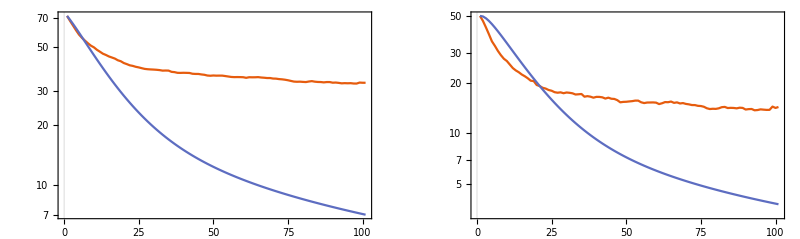

```mathematica
GraphicsRow[{
ListLogPlot[{meanAve,m1TrajTmp[[;;;;IntegerPart[1/dtMult]]]},ImageSize->400,Joined->True,PlotRange->{0,80}],
ListLogPlot[{nnAve,m2TrajTmp[[;;;;IntegerPart[1/dtMult]]]},ImageSize->400,Joined->True]
},ImageSize->800]
```

## Run

```mathematica
(* Number iterations *)
nIterBM=400; (* 50 *)
```

```mathematica
(* Batch size = number trials (i.e. dont rotate samples, just use all *)
nBatch=Length[trainingData];
```

```mathematica
(* Number gibbs sampling steps - doesn't matter if we evaluate h,j -> moments analytically *)
nGibbs=20;
```

```mathematica
(* Number basis funcs present *)
nBasis=5;
```

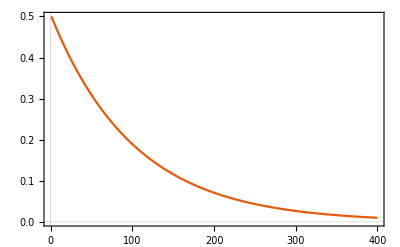

```mathematica
(* Learning rate *)
constLearningRateFlag=False;
lambdaMaxInit=0.5; (* 0.5 *)
lambdaMaxFinal=0.01; (* 0.01 *)
lambdaMax=Table[lambdaMaxInit*Exp[-(i-1)*Log[lambdaMaxInit/lambdaMaxFinal]/(nIterBM-1)],{i,1,nIterBM}];
ListLinePlot[lambdaMax]
```

```mathematica
(* Evaluate h,j -> moments analytically *)
analyticFlag=True;
```

```mathematica
(* Verbose flag *)
verboseFlag=False;
```

```mathematica
(* Lots of different IC *)
nIC=1;
```

```mathematica
(* Constant learning rate *)
lambdaMax=0.1;
constLearningRateFlag=True;

(* Regularization *)
lambdaReg=0.001;

theta0St=Association[];
thetaFinalSt=Association[];
thetaStSt=Association[];

Do[
(* Initial theta *)
theta0={kBranching,10.0,probAnnihilation/dt};
theta0+={RandomReal[{-0.1,0.1}*kBranching],RandomReal[{-0.1,0.1}*10.0],
RandomReal[{-0.1,0.1}*probAnnihilation/dt]};
theta0=Map[Max[0.0,#]&,theta0];
theta0St[iIC]=theta0;

(* Go *)
{thetaSt,varyh,varyj,meanAsleepFinal,nnAsleepFinal}=runBMOneTheta[trainingData,nIterBM,nBatch,nGibbs,nBasis,h0,j0,dt,tMax,nChain,lambdaMax,lambdaReg,theta0,analyticFlag,verboseFlag,constLearningRateFlag];

(* Store *)
thetaStSt[iIC]=thetaSt;
thetaFinalSt[iIC]=thetaSt[[-1]];
,{iIC,1,nIC}];
```

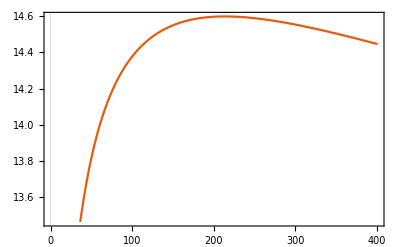

```mathematica
ListLinePlot[thetaSt[[;;,2]]]
```

```mathematica
theta0St
```

<|1→{9.85031,10.147,9.82589}|>

```mathematica
thetaFinalSt
```

<|1→{4.04052,14.4449,5.25375}|>

Plot style

```mathematica
SetOptions[ListLinePlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
SetOptions[ListContourPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
SetOptions[ListLogPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
colorFunc=("DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListContourPlot]));
```

Plots

```mathematica
timepts=Table[i,{i,0,tMax,dt}];
```

```mathematica
hRng=Range[-5,3.0,0.2];
jRng=Range[-1.0,4.0,0.1];
```

```mathematica
plthRng={-50,20.0};
pltjRng={-25,200};
```

### Initial basis function

```mathematica
{hTraj0,jTraj0}=fSolveTrajOneTheta[thetaSt[[1]],h0,j0,dt/10.0,tMax,True];
hTraj0=hTraj0[[;;;;10]];jTraj0=jTraj0[[;;;;10]];
```

```mathematica
tblFh0=Flatten[Table[{hVal,jVal,Dot[thetaSt[[1]],fBFsRed[hVal,jVal][[1]]]},{hVal,hRng},{jVal,jRng}],1];
tblFj0=Flatten[Table[{hVal,jVal,Dot[thetaSt[[1]],fBFsRed[hVal,jVal][[2]]]},{hVal,hRng},{jVal,jRng}],1];
```

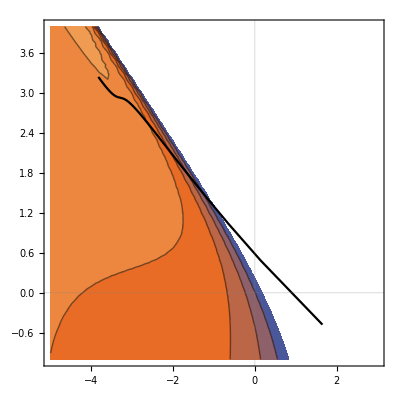

```mathematica
pltFh0=Show[
ListContourPlot[tblFh0,PlotTheme->"Scientific",ColorFunction->ColorData[{colorFunc,plthRng}],ColorFunctionScaling->False,PlotRange->plthRng],
ListLinePlot[Transpose[{hTraj0,jTraj0}],PlotStyle->Black,PlotRange->{{Min[hRng],Max[hRng]},{Min[jRng],Max[jRng]}}]
]
```

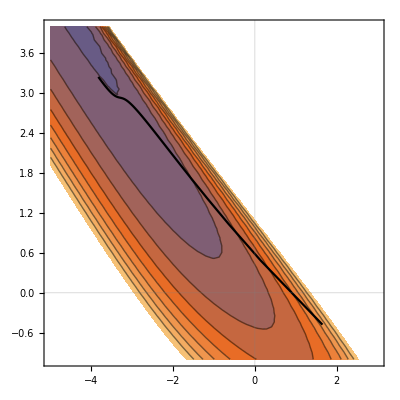

```mathematica
pltFj0=Show[
ListContourPlot[tblFj0,PlotTheme->"Scientific",ColorFunction->ColorData[{colorFunc,pltjRng}],ColorFunctionScaling->False,PlotRange->pltjRng],
ListLinePlot[Transpose[{hTraj0,jTraj0}],PlotStyle->Black,PlotRange->{{Min[hRng],Max[hRng]},{Min[jRng],Max[jRng]}}]
]
```

### Final basis function

```mathematica
{hTrajF,jTrajF}=fSolveTrajOneTheta[thetaSt[[-1]],h0,j0,dt/10.0,tMax,True];
hTrajF=hTrajF[[;;;;10]];
jTrajF=jTrajF[[;;;;10]];
```

```mathematica
tblFhF=Flatten[Table[{hVal,jVal,Dot[thetaSt[[-1]],fBFsRed[hVal,jVal][[1]]]},{hVal,hRng},{jVal,jRng}],1];
tblFjF=Flatten[Table[{hVal,jVal,Dot[thetaSt[[-1]],fBFsRed[hVal,jVal][[2]]]},{hVal,hRng},{jVal,jRng}],1];
```

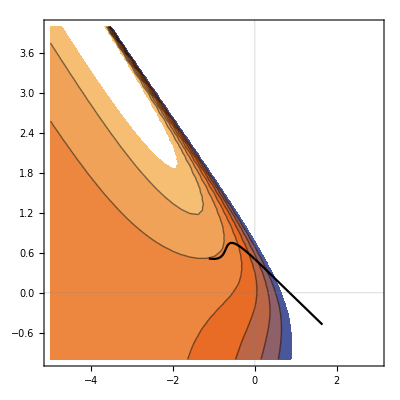

```mathematica
pltFhF=Show[
ListContourPlot[tblFhF,PlotTheme->"Scientific",ColorFunction->ColorData[{colorFunc,plthRng}],ColorFunctionScaling->False,PlotRange->plthRng],
ListLinePlot[Transpose[{hTrajF,jTrajF}],PlotStyle->Black,PlotRange->{{Min[hRng],Max[hRng]},{Min[jRng],Max[jRng]}}]
]
```

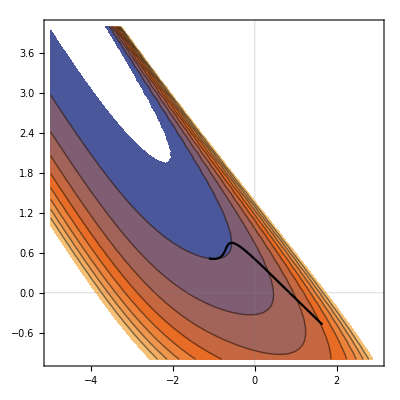

```mathematica
pltFjF=Show[
ListContourPlot[tblFjF,PlotTheme->"Scientific",ColorFunction->ColorData[{colorFunc,pltjRng}],ColorFunctionScaling->False,PlotRange->pltjRng],
ListLinePlot[Transpose[{hTrajF,jTrajF}],PlotStyle->Black,PlotRange->{{Min[hRng],Max[hRng]},{Min[jRng],Max[jRng]}}]
]
```

```mathematica
legh=BarLegend[{colorFunc,plthRng},LabelStyle->{FontSize->30}]
```

```mathematica
legj=BarLegend[{colorFunc,pltjRng},LabelStyle->{FontSize->30}]
```

### Export

```mathematica
Export["../figures_barw/fh_0.pdf",pltFh0];
Export["../figures_barw/fj_0.pdf",pltFj0];
Export["../figures_barw/fh_F.pdf",pltFhF];
Export["../figures_barw/fj_F.pdf",pltFjF];
```

```mathematica
Export["../figures_barw/fh_leg.pdf",legh];
Export["../figures_barw/fj_leg.pdf",legj];
```

### Final variational terms

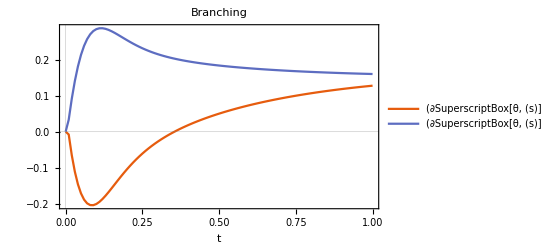

```mathematica
ListLinePlot[{
Transpose[{timepts,varyh[[;;,1]]}],
Transpose[{timepts,varyj[[;;,1]]}],
},FrameLabel->{"t"},PlotLabel->"Branching",PlotLegends->{"(∂SuperscriptBox[θ, (s)])/(∂h)","(∂SuperscriptBox[θ, (s)])/(∂J)"}]
```

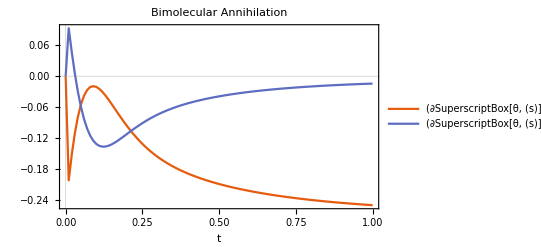

```mathematica
ListLinePlot[{
Transpose[{timepts,varyh[[;;,3]]}],
Transpose[{timepts,varyj[[;;,3]]}]
},FrameLabel->{"t"},PlotLabel->"Bimolecular Annihilation",PlotLegends->{"(∂SuperscriptBox[θ, (s)])/(∂h)","(∂SuperscriptBox[θ, (s)])/(∂J)"}]
```

### Plot theta

```mathematica
thetaSt[[-1]]
```

{4.04052,14.4449,5.25375}

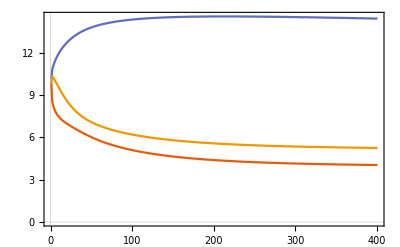

```mathematica
ListLinePlot[Table[thetaSt[[;;,i]],{i,1,Length[thetaSt[[-1]]]}]]
```

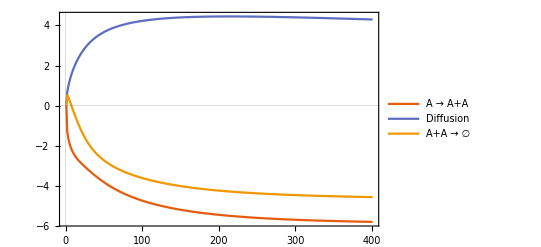

```mathematica
pltTheta=ListLinePlot[Table[thetaSt[[;;,i]]-thetaSt[[1,i]],{i,1,Length[thetaSt[[-1]]]}],PlotLegends->LineLegend[{"A → A+A","Diffusion","A+A → ∅"},LabelStyle->{FontSize->20}]]
```

### Export

```mathematica
Export["../figures_barw/theta.pdf",pltTheta];
```

### Plot moments

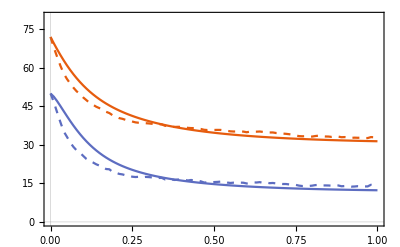

```mathematica
ListLinePlot[{Transpose[{timepts,meanAve}],Transpose[{timepts,meanAsleepFinal}],Transpose[{timepts,nnAve}],Transpose[{timepts,nnAsleepFinal}]},PlotRange->{0,80},PlotStyle->{{Dashed,colors[[1]]},{colors[[1]]},{Dashed,colors[[2]]},{colors[[2]]}}]
```

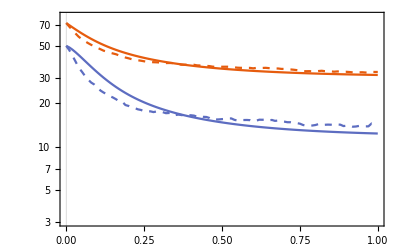

```mathematica
pltLogFinal=ListLogPlot[{Transpose[{timepts,meanAve}],Transpose[{timepts,meanAsleepFinal}],Transpose[{timepts,nnAve}],Transpose[{timepts,nnAsleepFinal}]},PlotRange->{3,80},PlotStyle->{{Dashed,colors[[1]]},{colors[[1]]},{Dashed,colors[[2]]},{colors[[2]]}},Joined->True]
```

```mathematica
meanAsleep0=Table[fMomentsFromhj[hTraj0[[i]],jTraj0[[i]],nChain][[1]],{i,1,Length[hTraj0]}];
nnAsleep0=Table[fMomentsFromhj[hTraj0[[i]],jTraj0[[i]],nChain][[2]],{i,1,Length[hTraj0]}];
```

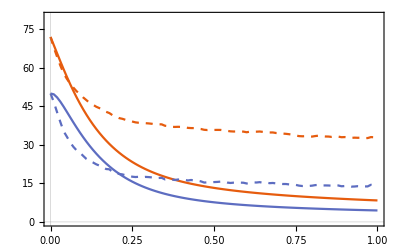

```mathematica
ListLinePlot[{Transpose[{timepts,meanAve}],Transpose[{timepts,meanAsleep0}],Transpose[{timepts,nnAve}],Transpose[{timepts,nnAsleep0}]},PlotRange->{0,80},PlotStyle->{{Dashed,colors[[1]]},{colors[[1]]},{Dashed,colors[[2]]},{colors[[2]]}}]
```

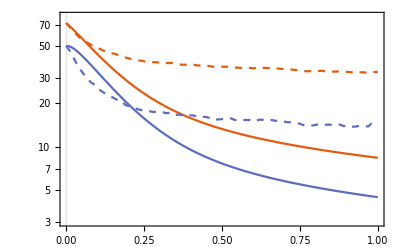

```mathematica
pltLogInit=ListLogPlot[{Transpose[{timepts,meanAve}],Transpose[{timepts,meanAsleep0}],Transpose[{timepts,nnAve}],Transpose[{timepts,nnAsleep0}]},PlotRange->{3,80},PlotStyle->{{Dashed,colors[[1]]},{colors[[1]]},{Dashed,colors[[2]]},{colors[[2]]}},Joined->True]
```

```mathematica
legMoments=LineLegend[{{Dashed,colors[[1]]},colors[[1]],{Dashed,colors[[2]]},colors[[2]]},{"Mean\n(stoch. sim)","Mean\n(asleep phase)","NN\n(stoch. sim)","NN\n(asleep phase)"},LabelStyle->{FontSize->20}]
```

### Export

```mathematica
Export["../figures_barw/log_init.pdf",pltLogInit];
Export["../figures_barw/log_final.pdf",pltLogFinal];
Export["../figures_barw/log_leg.pdf",legMoments];
```